## As always some code

```mathematica
SolutionMatrix[g_,sym_]:=Block[{mat,size, ordered},
size=VertexCount[g];
ordered=Flatten[SymbolToSets[sym]];
mat=Table[
Table[
If[row==col,2,
If[EdgeQ[g,row<->col],1,0]
]
,
{col,ordered}
]
,
{row,ordered}
];
mat
]
```

```mathematica
DrawSolutionMatrix[g_,sym_]:=Block[{mat=SolutionMatrix[g,sym], colors=SymbolToColoring[sym], labels, size, ordered, start,newBucket},
size=VertexCount[g];
ordered=Flatten[SymbolToSets[sym]];
labels=Table[{k,Block[{res=Style[ordered[[k]],Darker[(ordered[[k]]/.colors)]]},
res]},{k,size}];
start=1;
Table[
newBucket=Table[k,{k,start,start+Length[bucket]-1}];
start+=Length[bucket];
Table[
Table[
mat[[row2,col2]]+=.1
,{col2,newBucket}
]
,{row2,newBucket}
]
,{bucket,SymbolToSets[sym]}
];
Column[
{
(*Graph[g,ImageSize->500,VertexStyle->colors]
,*)
MatrixPlot[ mat,Mesh->All, ImageSize->250,FrameTicks->{labels,labels,labels,labels}]
}
]
]
```

```mathematica
ContractMat[mat_, row_, col_]:=Block[{ matJoin, matContract,fromVertexToVertexSet,vertexSets,rowBucket,colBucket, max, max2, size},
size=Length[mat];
vertexSets=Table[{i},{i,size}];
If[mat[[row,col]]==0,
matJoin=mat;
matContract=mat;

(* first compute to which vertex set row and column belong*)
fromVertexToVertexSet=Association[];
Table[Table[fromVertexToVertexSet[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
rowBucket=vertexSets[[fromVertexToVertexSet[row]]];
colBucket=vertexSets[[fromVertexToVertexSet[col]]];

(* now set the entries in contract and joined *)
Table[
matContract[[r,c]]=2;
matContract[[c,r]]=2;
matJoin[[r,c]]=1;
matJoin[[c,r]]=1
,
{r,rowBucket},
{c,colBucket}
];
(* now make sure the entries are consistent.  We take the max of the other entries *)
Table[
max=Max[Table[matContract[[r,v]],{r, rowBucket}]];
max2=Max[Table[matContract[[r,v]],{r, colBucket}]];
max=Max[max,max2];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, rowBucket}];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, colBucket}];
,
{v,size}
];

];
matContract
]
```

## Calculating starts here

```mathematica
Length[FindFullFormula4[Graph[plantri[[1]]]]]
```

10

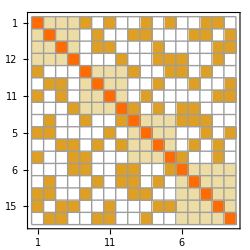
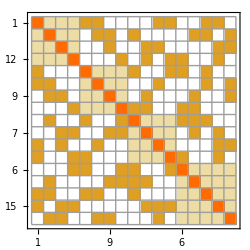
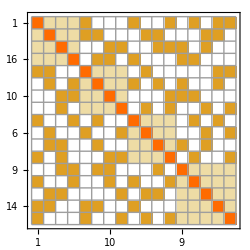
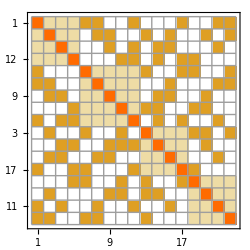
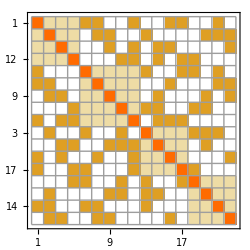
{-Graphics-14ac♁29bd♁357h♁68efg,-Graphics-14ac♁259d♁37bh♁68efg,-Graphics-137g♁24ac♁568f♁9bdeh,-Graphics-14ac♁259df♁37gh♁68be,-Graphics-14ac♁259df♁37bh♁68eg}

```mathematica
Table[Labeled[DrawSolutionMatrix[plantri8,sol],SymbolToLabel[sol]],{sol,Take[FindFullFormula4[plantri8],5]}]
```

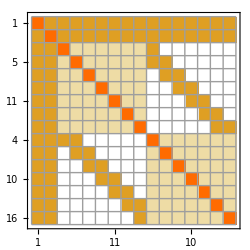
{-Graphics-1♁2♁3579bdf♁468aceg}

```mathematica
With[
{g=MinimalGraph[15]},
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,FindFullFormula4[g]}]
]
```

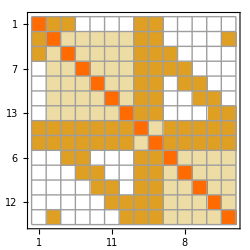
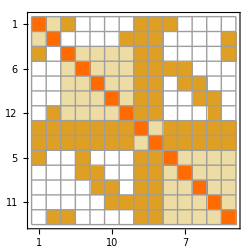
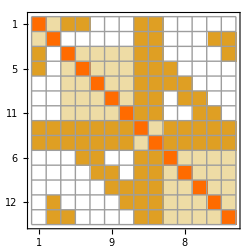
{-Graphics-1♁2579bd♁34♁68ace,-Graphics-1d♁268ac♁34♁579be,-Graphics-1d♁2579b♁34♁68ace}

```mathematica
With[
{g=JacobsThalGraph[10]},
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,Take[FindFullFormula4[g],3]}]
]
```

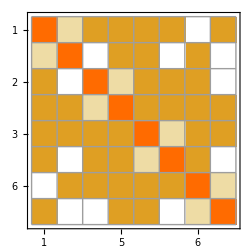
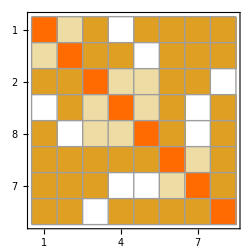
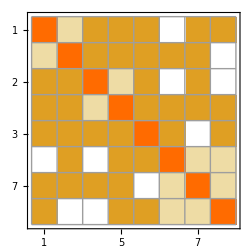
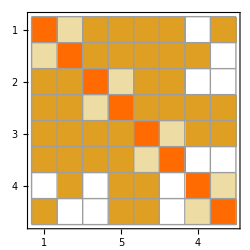
{-Graphics-14♁25♁37♁68,-Graphics-16♁248♁37♁5,-Graphics-16♁25♁3♁478,-Graphics-16♁25♁37♁48}

```mathematica
With[
{g=ReadGrof[20]},
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,FindFullFormula4[g]}]
]
```

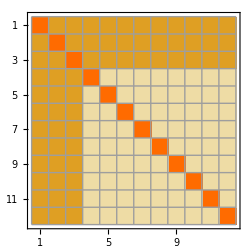
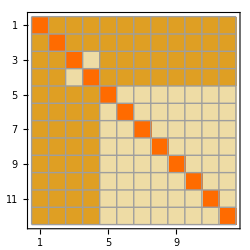
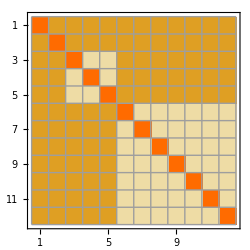
{{-Graphics-1♁2♁3♁456789abc},{-Graphics-1♁2♁34♁56789abc},{-Graphics-1♁2♁345♁6789abc}}

```mathematica
Map[With[
{g=#},
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,FindFullFormula4[g]}]
]&,Take[BarelyFourColorableGraphsOfCount[12],3]
]
```

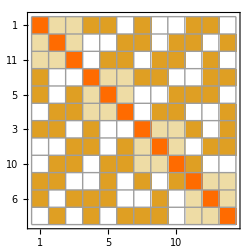
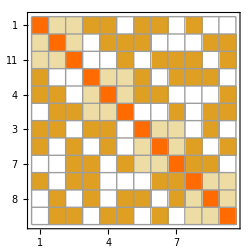
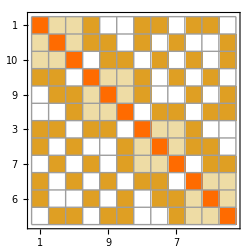
{-Graphics-19b♁25c♁37a♁468,-Graphics-19b♁24c♁357♁68a,-Graphics-18a♁29b♁357♁46c}

```mathematica
With[
{g=Graph[plantri[[1]]]},
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,Take[FindFullFormula4[g],3]}]
]
```

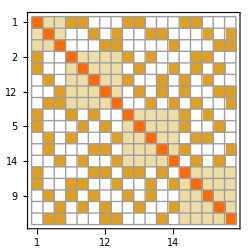
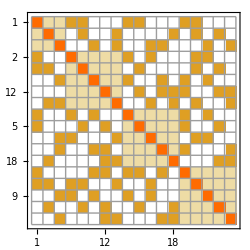
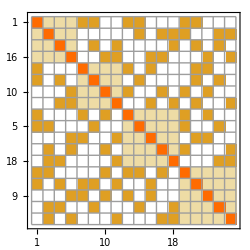
{-Graphics-1gi♁26acf♁358be♁479dh,-Graphics-1eg♁26acf♁358bi♁479dh,-Graphics-1ceg♁26af♁358bi♁479dh}

```mathematica
With[
{g=Graph[plantri[[20]]]},
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,Take[FindFullFormula4[g],3]}]
]
```